```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*tϕ=ts/200;
αϕ=α/200;*)
tϕ1=0.2ts;
tϕ2=0.2ts;
θ1=0.0π;

(*spin orbit angle can be overcome by a phase shift in the Middle region!*)
θM=0.5π;
ϕscM=0.5 π;

θ2=1.0 π;
ϕ2=0.0π;
ϕα2=1.0 π;
ϕsc2=0.0 π;
```

```mathematica
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕscM)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕscM)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2](Cos[ϕ2]+ⅈ Sin[ϕ2]),Band[{1,2}]->(Cos[ϕα2]-ⅈ Sin[ϕα2])α/2,Band[{2,1}]->(-Cos[ϕα2]+ⅈ Sin[ϕα2])α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2](Cos[ϕ2]-ⅈ Sin[ϕ2]),Band[{1,2}]->(-Cos[ϕα2]-ⅈ Sin[ϕα2])α/2,Band[{2,1}]->(Cos[ϕα2]+ⅈ Sin[ϕα2])α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕsc2)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕsc2)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0},{HM1,HMM,HM2},{0,H2M,H22}}]];
```

```mathematica
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[Hsp,-10]]]];
```

```mathematica
n=5;
e[[n]]
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];




e[[n-1]]
ψB1ue=Table[{i-1,Abs[ψ[[n-1,i]]]},{i,1,Nx}];
ψBMue=Table[{i-1-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx,4Nx+NxM}];
ψB2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
```

-8.80912×10^-12

-0.00678869

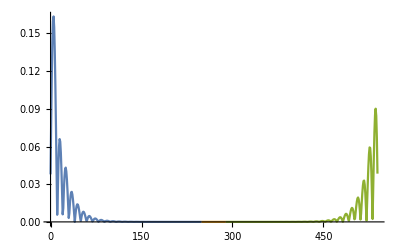

```mathematica
ListPlot[{ψA1ue,ψAMue,ψA2ue},Joined->True,PlotRange->All]
```

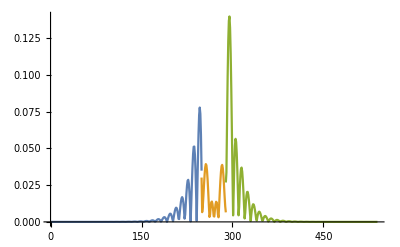

```mathematica
ListPlot[{ψB1ue,ψBMue,ψB2ue},Joined->True,PlotRange->All]
```